# Google PageRankとは

ウェブページの重要度を決定するためのアルゴリズム、またはそれによるランキングのこと

次の条件を考慮して、初期の重み無しリンクのネットワーク状態から重みつきリンクのネットワーク状態を計算することで得られる

注目に値する重要なウェブページはたくさんのページからリンクされると考えられる

重要なページからのリンクは価値が高いと考えられる

乱発されたリンクにはあまり価値がないと考えられる

リンク以外の情報によりすべてのページにたどり着く可能性がある(ランダムサーファーモデル)

http://ja.wikipedia.org/wiki/%E3%83%9A%E3%83%BC%E3%82%B8%E3%83%A9%E3%83%B3%E3%82%AF より

## Nav: top | next

## 図: ネットワーク状態の変化:

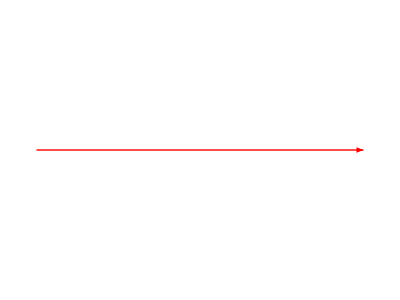
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

## See also

Hitsアルゴリズム

以上webコンテンツ

## Program

```mathematica
toAdjacency[t_]:=Map[If[#>0,1,0]&,t,{2}]
```

```mathematica
ellipseLayout[n_,{a_,b_}]:=Table[{a Cos[2Pi/n u],b Sin[2Pi/n u]},{u,1,n}]
```

```mathematica
MtoH[m_]:=Map[If[Tr[#]==0,#,#/Tr[#]]&,m]
```

```mathematica
MtoS[m_]:=Module[{l},
l=Dimensions[m][[2]];
Map[If[Tr[#]==0,Table[1/l,{l}],#/Tr[#]]&,m]
]
```

```mathematica
StoG[m_,a_]:=m*a+(1-a)/Length[m]
```

```mathematica
MtoG[m_,a_]:=MtoS[m]*a+(1-a)/Length[m]
```

```mathematica
nextScore[score_,m_]:=Map[Tr[#]&,Transpose[m*score]]
```

```mathematica
zeroSelf[mat_]:=ReplacePart[mat,Table[{n,n}->0,{n,Length[mat]}]]
```

## 定義と例示

nextScore[]の繰り返し適応によるscoreの収束によって返されるベクトルの各要素が言わば、各ページのスコアです。このスコアが高いほど影響力が高いとされます。MtoH[]とStoG[]のaに注目してみましょう。この操作により、もとが疎行列であってもスコアの低いページのスコアが0に落ち込むことを防ぎます。これはランダムサーファーモデルと言われています。

早速、例を見てみます。ノード数を8として、ランダムに隣接行列を作成します。自身へのリンクは0に置き換えています。

```mathematica
l={{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,0},{0,1,1,1,0,1,0,0}}
```

{{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,0},{0,1,1,1,0,1,0,0}}

```mathematica
vlabels["l"]=Table[n->Text[Style[IntegerString[n,"Roman"],Large]],{n,Length[l]}]
```

{1→I,2→II,3→III,4→IV,5→V,6→VI,7→VII,8→VIII}

```mathematica
(*(l=ReplacePart[Table[RandomChoice[{1,0,0,0,0}],{8},{8}],Table[{n,n}->0,{n,8}]])//TableForm*)
```

以下は隣接行列からのグラフ表示です。

```mathematica
gr["m"]=AdjacencyGraph[l,VertexCoordinates->ellipseLayout[8,{1.4,1}],VertexLabels->vlabels["l"],ImagePadding->{{10,40},{10,50}},ImageSize->{300,300}]
```

-Graphics-

下記により各ノードのスコアを求めます。スコアの初期値を全て1/8とします。50回の繰り返しで十分に収束します。

```mathematica
PGscore["l"]=Nest[nextScore[#,MtoG[l,0.9]]&,Table[1/8,{8}],50]
```

{0.187836,0.138007,0.248609,0.0795569,0.0649444,0.0795569,0.136546,0.0649444}

また、この値は主固有ベクトルの値と一致します。

```mathematica
Map[#/Tr[#]&,Eigensystem[Transpose[MtoG[l,0.9]]][[2]][[1]],{0}]
```

{0.187836,0.138007,0.248609,0.0795569,0.0649444,0.0795569,0.136546,0.0649444}

Π^T= Π^T.G の確認:

```mathematica
PGscore["l"].MtoG[l,0.9]
```

{0.187836,0.138007,0.248609,0.0795569,0.0649444,0.0795569,0.136546,0.0649444}

G × Π^T の強度が  Π^Tになることの確認:

```mathematica
(fixedtable["l"]=MtoG[l,0.9]*PGscore["l"])//TableForm
```

0.00234794 | 0.00234794 | 0.1714 | 0.00234794 | 0.00234794 | 0.00234794 | 0.00234794 | 0.00234794
0.0172509 | 0.0172509 | 0.0172509 | 0.0172509 | 0.0172509 | 0.0172509 | 0.0172509 | 0.0172509
0.0310761 | 0.0310761 | 0.0310761 | 0.0310761 | 0.0310761 | 0.0310761 | 0.0310761 | 0.0310761
0.00994462 | 0.00994462 | 0.00994462 | 0.00994462 | 0.00994462 | 0.00994462 | 0.00994462 | 0.00994462
0.000811806 | 0.0592618 | 0.000811806 | 0.000811806 | 0.000811806 | 0.000811806 | 0.000811806 | 0.000811806
0.000994462 | 0.000994462 | 0.000994462 | 0.000994462 | 0.000994462 | 0.000994462 | 0.0725957 | 0.000994462
0.124598 | 0.00170682 | 0.00170682 | 0.00170682 | 0.00170682 | 0.00170682 | 0.00170682 | 0.00170682
0.000811806 | 0.0154243 | 0.0154243 | 0.0154243 | 0.000811806 | 0.0154243 | 0.000811806 | 0.000811806

```mathematica
Map[Tr[#]&,fixedtable["l"]]
```

{0.187836,0.138007,0.248609,0.0795569,0.0649444,0.0795569,0.136546,0.0649444}

```mathematica
Map[Tr[#]&,Transpose[fixedtable["l"]]]
```

{0.187836,0.138007,0.248609,0.0795569,0.0649444,0.0795569,0.136546,0.0649444}

```mathematica
edgeforce["l"]=MapIndexed[If[#>0,{#2,#1}]&,fixedtable["l"],{2}];
```

```mathematica
(edgeforcelabels["l"]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Text[Style[ToString[ Round[#[[2]],0.001] ],Medium]])&,Cases[edgeforce["l"],_List,{2}]])//Short
```

{1->1→0.002,1->2→0.002,1->3→0.171,1->4→0.002,1->5→0.002,1->6→0.002,1->7→0.002,1->8→0.002,2->1→0.017,2->2→0.017,2->3→0.017,«42»,7->6→0.002,7->7→0.002,7->8→0.002,8->1→0.001,8->2→0.015,8->3→0.015,8->4→0.015,8->5→0.001,8->6→0.015,8->7→0.001,8->8→0.001}

```mathematica
style["l"]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Thickness[#[[2]]/10])&,Cases[edgeforce["l"],_List,{2}]];
```

```mathematica
gr["l",1]=AdjacencyGraph[toAdjacency[fixedtable["l"]],VertexCoordinates->ellipseLayout[8,{1.4,1}],DirectedEdges->True,VertexLabels->vlabels["l"],EdgeStyle->style["l"],(*EdgeLabels->edgeforcelabels["l"],*)ImagePadding->{{5,5},{0,5}},ImageSize->{360,360}]
```

-Graphics-

```mathematica
gr["l",1,"labeled"]=AdjacencyGraph[toAdjacency[fixedtable["l"]],VertexCoordinates->ellipseLayout[8,{1.4,1}],DirectedEdges->True,VertexLabels->vlabels["l"],EdgeStyle->style["l"],EdgeLabels->edgeforcelabels["l"],ImagePadding->{{5,5},{0,5}},ImageSize->{360,600}]
```

-Graphics-

```mathematica
txtG=.
```

```mathematica
txtG["m"]=Graphics[Text[Style["初期状態のネットワーク",Large]],ImageSize->{300,30}]
```

-Graphics-

```mathematica
txtG["l"]=Graphics[Text[Style["最終状態のネットワーク",Large]],ImageSize->{300,30}]
```

-Graphics-

```mathematica
txtG["middle"]=Graphics[Text[Style[" ",Large]],ImageSize->{40,30}]
```

-Graphics-

```mathematica
arr=Graphics[{Red,Arrowheads[0.1],Arrow[{{0,0},{0.5,0}}]}]
```

-Graphics-

```mathematica
Grid[{{gr["m"],arr,gr["l",1]},{txtG["m"],txtG["middle"],txtG["l"]}}]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

## Pagerankアルゴリズムの引用/被引用行列への応用

```mathematica
numofnodes=4
```

4

```mathematica
toAdjacency[t_]:=Map[If[#>0,1,0]&,t,{2}]
```

引用被引用行列の設定

```mathematica
c={{0,0,0,3},{1,0,0,0},{2,2,0,0},{0,3,1,0}}
```

{{0,0,0,3},{1,0,0,0},{2,2,0,0},{0,3,1,0}}

```mathematica
(*(c=ReplacePart[Table[RandomChoice[{3,2,1,0,0,0,0}],{numofnodes},{numofnodes}],Table[{n,n}->0,{n,numofnodes}]])//TableForm*)
```

```mathematica
nodename=Table[IntegerString[n,"Roman"],{n,numofnodes}]
```

{I,II,III,IV}

```mathematica
vlabels[4]=Table[n->Text[Style[IntegerString[n,"Roman"],Large]],{n,numofnodes}]
```

{1→I,2→II,3→III,4→IV}

### アニメーションのコマ作成

スライド1

```mathematica
edgeforce[0]=MapIndexed[If[#>0,{#2,#1}]&,c,{2}]
```

{{Null,Null,Null,{{1,4},3}},{{{2,1},1},Null,Null,Null},{{{3,1},2},{{3,2},2},Null,Null},{Null,{{4,2},3},{{4,3},1},Null}}

```mathematica
edgeforcelabels[0]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Text[Style[ToString[#[[2]]],Medium]])&,Cases[edgeforce[0],_List,{2}]]
```

{1->4→3,2->1→1,3->1→2,3->2→2,4->2→3,4->3→1}

```mathematica
style[0]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Thickness[#[[2]]/100])&,Cases[edgeforce[0],_List,{2}]]
```

{1->4→Thickness[3/100],2->1→Thickness[1/100],3->1→Thickness[1/50],3->2→Thickness[1/50],4->2→Thickness[3/100],4->3→Thickness[1/100]}

```mathematica
gr[0]=AdjacencyGraph[toAdjacency[c],VertexLabels->vlabels[4],EdgeLabels->edgeforcelabels[0],EdgeStyle->style[0],ImagePadding->{{0,30},{0,30}},ImageSize->{240,240}]
```

-Graphics-

```mathematica
edgeforcelabels[0]
```

{1->4→3,2->1→1,3->1→2,3->2→2,4->2→3,4->3→1}

```mathematica
tf[0]=TableForm[Map[Text[Style[ToString[#],Medium]]&,c,{2}],TableHeadings->{nodename,nodename}]
```

| I | II | III | IV
I | 0 | 0 | 0 | 3
II | 1 | 0 | 0 | 0
III | 2 | 2 | 0 | 0
IV | 0 | 3 | 1 | 0

```mathematica
tx[0]=Graphics[{FontSize->14,Text[Style["基となる引用被引用行列",TextAlignment->Left]]}];
```

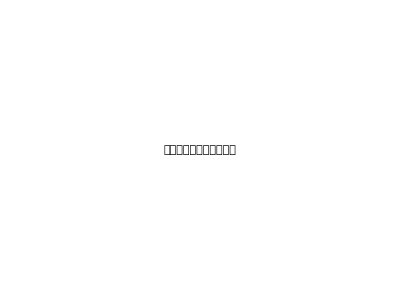
-Graphics- | -Graphics-
 | I | II | III | IV
I | 0 | 0 | 0 | 3
II | 1 | 0 | 0 | 0
III | 2 | 2 | 0 | 0
IV | 0 | 3 | 1 | 0 |

```mathematica
Grid[{{gr[0],tx[0]},{tf[0],SpanFromAbove}},ItemSize->{{1->27,2->14},{1->10,2->10}},Alignment->{{Center,Left},{Center,Left}},Spacings->{{1,0},{0,0}},Frame->True]
```

スライド2

```mathematica
m[1]=MtoG[c,0.9]
```

{{0.025,0.025,0.025,0.925},{0.925,0.025,0.025,0.025},{0.475,0.475,0.025,0.025},{0.025,0.7,0.25,0.025}}

```mathematica
edgeforce[1]=MapIndexed[If[#>0,{#2,#1}]&,m[1],{2}]
```

{{{{1,1},0.025},{{1,2},0.025},{{1,3},0.025},{{1,4},0.925}},{{{2,1},0.925},{{2,2},0.025},{{2,3},0.025},{{2,4},0.025}},{{{3,1},0.475},{{3,2},0.475},{{3,3},0.025},{{3,4},0.025}},{{{4,1},0.025},{{4,2},0.7},{{4,3},0.25},{{4,4},0.025}}}

```mathematica
edgeforcelabels[1]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Text[Style[ToString[#[[2]]],Medium]])&,Cases[edgeforce[1],_List,{2}]]
```

{1->1→0.025,1->2→0.025,1->3→0.025,1->4→0.925,2->1→0.925,2->2→0.025,2->3→0.025,2->4→0.025,3->1→0.475,3->2→0.475,3->3→0.025,3->4→0.025,4->1→0.025,4->2→0.7,4->3→0.25,4->4→0.025}

```mathematica
style[1]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Thickness[#[[2]]/50])&,Cases[edgeforce[1],_List,{2}]]
```

{1->1→Thickness[0.0005],1->2→Thickness[0.0005],1->3→Thickness[0.0005],1->4→Thickness[0.0185],2->1→Thickness[0.0185],2->2→Thickness[0.0005],2->3→Thickness[0.0005],2->4→Thickness[0.0005],3->1→Thickness[0.0095],3->2→Thickness[0.0095],3->3→Thickness[0.0005],3->4→Thickness[0.0005],4->1→Thickness[0.0005],4->2→Thickness[0.014],4->3→Thickness[0.005],4->4→Thickness[0.0005]}

```mathematica
toAdjacency[m[1]]
```

{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}}

```mathematica
gr[1]=AdjacencyGraph[toAdjacency[MtoG[c,0.9]],DirectedEdges->True,VertexLabels->vlabels[4],EdgeStyle->style[1],(*EdgeLabels->edgeforcelabels[1],*)ImagePadding->{{5,5},{0,5}},ImageSize->{300,300}]
```

-Graphics-

```mathematica
tx[1]=Graphics[{FontSize->14,Text[Style["ランダムサーファーモデル
による結合行列",TextAlignment->Left]]}];
```

```mathematica
tf[1]=TableForm[Map[Text[Style[ToString[#],Medium]]&,m[1],{2}],TableHeadings->{nodename,nodename}]
```

| I | II | III | IV
I | 0.025 | 0.025 | 0.025 | 0.925
II | 0.925 | 0.025 | 0.025 | 0.025
III | 0.475 | 0.475 | 0.025 | 0.025
IV | 0.025 | 0.7 | 0.25 | 0.025

```mathematica
sc[1]=Table[1/numofnodes,{numofnodes}]
```

{1/4,1/4,1/4,1/4}

```mathematica
sct[1]=TableForm[Transpose[{sc[1]}]//N,TableHeadings->{nodename,{"点数"}}]
```

| 点数
I | 0.25
II | 0.25
III | 0.25
IV | 0.25

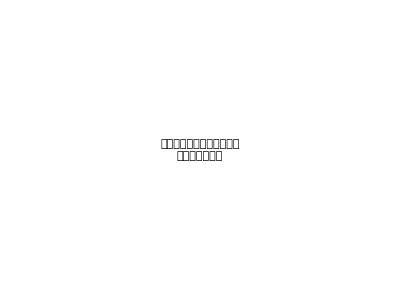
-Graphics- | -Graphics-
 | I | II | III | IV
I | 0.025 | 0.025 | 0.025 | 0.925
II | 0.925 | 0.025 | 0.025 | 0.025
III | 0.475 | 0.475 | 0.025 | 0.025
IV | 0.025 | 0.7 | 0.25 | 0.025 |  | 点数
I | 0.25
II | 0.25
III | 0.25
IV | 0.25

```mathematica
Grid[{{gr[1],tx[1]},{tf[1],sct[1]}},ItemSize->{{1->27,2->14},{1->10,2->10}},Alignment->{{Center,Left},{Center,Left}},Spacings->{{1,0},{0,0}},Frame->True]
```

スライド last

```mathematica
m[1]=MtoG[c,0.9]
```

{{0.025,0.025,0.025,0.925},{0.925,0.025,0.025,0.025},{0.475,0.475,0.025,0.025},{0.025,0.7,0.25,0.025}}

```mathematica
PGscore["m[5]"]=Nest[nextScore[#,MtoG[m[1],0.9]]&,Table[1/numofnodes,{numofnodes}],5]
```

{0.323921,0.259697,0.103197,0.313185}

```mathematica
PGscore["m[25]"]=Nest[nextScore[#,MtoG[m[1],0.9]]&,Table[1/numofnodes,{numofnodes}],25]
```

{0.314234,0.275071,0.108688,0.302006}

```mathematica
PGscore["m[50]"]=Nest[nextScore[#,MtoG[m[1],0.9]]&,Table[1/numofnodes,{numofnodes}],50]
```

{0.314268,0.275009,0.108666,0.302057}

```mathematica
PGscore["m[100]"]=Nest[nextScore[#,MtoG[m[1],0.9]]&,Table[1/numofnodes,{numofnodes}],100]
```

{0.314267,0.275009,0.108666,0.302057}

```mathematica
Tr[PGscore["m[50]"]]
```

1.

```mathematica
PGscore["m[100]"].MtoG[m[1],0.9]
```

{0.314267,0.275009,0.108666,0.302057}

```mathematica
(fixedtable["m[100]"]=MtoG[m[1],0.9]*PGscore["m[100]"])//TableForm
```

0.0149277 | 0.0149277 | 0.0149277 | 0.269484
0.235821 | 0.0130629 | 0.0130629 | 0.0130629
0.0491716 | 0.0491716 | 0.00516166 | 0.00516166
0.0143477 | 0.197847 | 0.0755142 | 0.0143477

```mathematica
Map[Tr[#]&,Transpose[fixedtable["m[100]"]]]
```

{0.314267,0.275009,0.108666,0.302057}

```mathematica
edgeforce["last"]=MapIndexed[If[#>0,{#2,#1}]&,fixedtable["m[100]"],{2}]
```

{{{{1,1},0.0149277},{{1,2},0.0149277},{{1,3},0.0149277},{{1,4},0.269484}},{{{2,1},0.235821},{{2,2},0.0130629},{{2,3},0.0130629},{{2,4},0.0130629}},{{{3,1},0.0491716},{{3,2},0.0491716},{{3,3},0.00516166},{{3,4},0.00516166}},{{{4,1},0.0143477},{{4,2},0.197847},{{4,3},0.0755142},{{4,4},0.0143477}}}

```mathematica
edgeforcelabels["last"]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Text[Style[ToString[Round[#[[2]],0.001]],Medium]])&,Cases[edgeforce["last"],_List,{2}]]
```

{1->1→0.015,1->2→0.015,1->3→0.015,1->4→0.269,2->1→0.236,2->2→0.013,2->3→0.013,2->4→0.013,3->1→0.049,3->2→0.049,3->3→0.005,3->4→0.005,4->1→0.014,4->2→0.198,4->3→0.076,4->4→0.014}

```mathematica
style["last"]=Map[(DirectedEdge[#[[1,1]],#[[1,2]]]->Thickness[#[[2]]/25])&,Cases[edgeforce["last"],_List,{2}]]
```

{1->1→Thickness[0.000597108],1->2→Thickness[0.000597108],1->3→Thickness[0.000597108],1->4→Thickness[0.0107794],2->1→Thickness[0.00943282],2->2→Thickness[0.000522518],2->3→Thickness[0.000522518],2->4→Thickness[0.000522518],3->1→Thickness[0.00196686],3->2→Thickness[0.00196686],3->3→Thickness[0.000206466],3->4→Thickness[0.000206466],4->1→Thickness[0.000573908],4->2→Thickness[0.00791388],4->3→Thickness[0.00302057],4->4→Thickness[0.000573908]}

```mathematica
gr[1]=AdjacencyGraph[toAdjacency[fixedtable["m[100]"]],DirectedEdges->True,VertexLabels->vlabels[4],EdgeStyle->style["last"],(*EdgeLabels->edgeforcelabels["last"],*)ImagePadding->{{5,5},{0,5}},ImageSize->{300,300}]
```

-Graphics-

```mathematica
gr[1]=AdjacencyGraph[toAdjacency[fixedtable["m[100]"]],DirectedEdges->True,VertexLabels->vlabels[4],EdgeStyle->style["last"],EdgeLabels->edgeforcelabels["last"],ImagePadding->{{5,5},{0,5}},ImageSize->{300,300}]
```

-Graphics-

## 作業メモおよび確認

スコアの算出

```mathematica
PGscore["c"]=Nest[nextScore[#,MtoG[c,0.9]]&,Table[1/numofnodes,{numofnodes}],40]
```

{0.317192,0.277365,0.0948946,0.310549}

```mathematica
Map[#/Tr[#]&,Eigensystem[Transpose[MtoG[c,0.9]]][[2]][[1]],{0}]
```

{0.317272,0.27731,0.0948726,0.310545}

収束していることの確認

```mathematica
PGscore["c"].MtoG[c,0.9]
```

{0.317331,0.277323,0.0948734,0.310472}

```mathematica
Map[Tr[#]&,MtoG[c,0.9]*PGscore["c"]]
```

{0.317192,0.277365,0.0948946,0.310549}

重みつき引用被引用行列

```mathematica
MtoG[c,0.9]*PGscore["c"]//TableForm
```

0.00792979 | 0.00792979 | 0.00792979 | 0.293402
0.256563 | 0.00693413 | 0.00693413 | 0.00693413
0.045075 | 0.045075 | 0.00237237 | 0.00237237
0.00776371 | 0.217384 | 0.0776371 | 0.00776371

```mathematica
{{a,b},{k,d}}*{e,f}
```

{{a e,b e},{f k,d f}}

```mathematica
gr[1]=AdjacencyGraph[toAdjacency[MtoG[c,0.9]],DirectedEdges->True,VertexLabels->vlabels[4],EdgeStyle->style[1],EdgeLabels->edgeforcelabels[1],ImagePadding->{{0,30},{0,30}},ImageSize->{400,220}]
```

-Graphics-